# Mathematica Write-Up Guide for E1

Before working this tutorial, you may want to familiarize yourself with how Mathematica works for a little bit. Try making a few simple calculations and get used to the formatting and the “shift return” evaluation. This tutorial is meant to guide you through writing your lab report in the context of PHYS 1140, not give you a general overview of how Mathematica functions and all of its amazing features.

For lab reports in the future refer to the additional Mathematica tutorial we have provided online to perform additional tasks.

## Saving your Work:

Log on to the computers using your CU Boulder identikey and identikey password.

Save a temporary copy to the desktop of your computer. Once you lab session is over, we recommend saving your work to a USB flash drive, emailing it to yourself, Google Drive, etc... The more places the better, as this will avoid possible heart ache in the future. Once you log-off you may not be able to retrieve your previous work.

## Cells in Mathematica:

Mathematica consists of “cells” that are indicated on the right side of the document by a tiered bracketing system. Each cell has a defined format that can be chosen by clicking on the “Format” tab and going to “Style”. This brings up a menu of all the styles that can be defined for a cell. For example the cell that this text exists in is the “Text” style. The default style is the “Input” style. The styles you will use most are as follows: Title, Subtitle, Section, Subsection, Input, Output.  First title your Mathematica document as “E1: Introduction to Circuits” by clicking the Format tab and choosing “Title” from the Style menu. Be sure to include your name, T.A.’s name, section number, and date. Then, with your mouse place the cursor below your title until the cursor becomes horizontal and click there. This creates a new input cell. 

You will use input cells to make calculations and write code for tables and plots, and use text cells for reporting your analysis, observations, and results of an experiment. It is important that you do not write text in an input cell as this will cause many problems when you evaluate and edit your notebook.

Note that on the right side of the cell there are brackets. By right clicking on the cell bracket you can change the properties and style of that cell or group of cells, in addition to copying and pasting, and a variety of other features.

## Making Page Headers in Mathematica:

You will be required to make a “header” for all of your documents/reports for PHYS 1140. This ensures your name is on all pages and can be returned to you or your T.A. if pages get separated or turned into the wrong turn-in slot. To make a header follow these steps:
	1) Click “File”.
	2) Click on “Printing Settings”.
	3) Click on “Headers and Footers” which will take you to the header and footer menu.
	4) Enter the appropriate Information into the header field for both the left and right pages. Place the header on the right side of the page.
	5) Click on “Options”.
	6) Make sure the box for “Facing pages with the first Page on the” is not checked, but select “Right”.
	7) On the “Include on first page” select “Header”.

## Write Your Introduction!

In the following sections we will go over how to make calculations and format data. Put the section title in a “Section” cell, and write the body of your introduction in a “Text” cell below that.Given what you now know, start by writing your introduction section and part of your data analysis.

To spell check your document, something you will want to do when you are finished writing a report, go to the “Edit” menu and click on “Check Spelling...”. Be sure to do this when you are all done with your report! ☺

## Inputting Data in Mathematica

For your PHYS 1140 lab reports, you will be inputting data in one of two different ways: individual numbers or as a list. In this first example, we will enter data for the cold resistance of the light bulb and perform a simple computation.

Before writing the code, take note of the following items:
	- Input cells are evaluated by pressing and holding: shift return. Unassigned variables are blue and assigned variables are black. 
	- Notice that the semicolon ; suppresses the output, i.e. Mathematica assigns the variable a value but does not print it in the output.
	- Comments are made by: (* blah blah blah *) which allows you to give an explanation of the variable name and provide units. Note that comments are not printed in the output.
	- Greek letters, and other special characters, like δ are made by pressing: esc delta esc. Also the square root symbol is made by pressing ctrl 2 to get √□. The esc key in Mathematica is often used as a keyboard shortcut for making Greek letters and special characters. You will learn these as the semester goes on. For now go to “Palettes” and click on “Classroom Assistant” and look through some of the functional and typesetting features in this palette. To get Greek letters toggle the “Typesetting” pull-down menu and click on the “∞ β” button. (Tip: If you hover your cursor over the symbol, the keyboard shortcut appears.)
	- The output is unrounded, so final answers must be reported in a text cell. 
	- Values and their uncertainties must be written separately in input cells (i.e. you do not write “Rsystem = 1.3 +± 0.1” in an input cell). Mathematica can not perform arithmetic consistently on a number like this.
	- Do not use subscripts, underscores, or spaces when creating a variable name (i.e. you do not write “Rsystem=1.3” or “R_system=1.3” or “Resistance system = 1.3”). Be careful using capital letters as well since they may already be built-in functions in Mathematica. (i.e. the function N[] turns a number, like Sin[4/3], into a decimal. Typing “N=32” will cause issues.)
	
Type the following into an input cell using the measured cold resistance that you collected and press the Shift key (hold it down) and press the enter key.

```mathematica
Rsystem = 1.3; (*Bulb+Wire resistance in Ohms*) 
Rwires = 0.4; (*Resistance of the wires in Ohms*)
δR = 0.1; (*Uncertianty on the DMM in Ohms*)
Rbulb = Rsystem-Rwires (*Resistance of the bulb in Ohms*)
δRbulb = √(δR^2+δR^2)(*Uncertianty of the resistance in Ohms*)
```

0.9

0.141421

Hence my measured resistance with the DMM, reported in standard format, is: R = (0.90 ± 0.14) Ω.

## Tables and Plotting in Mathematica

In your E1 experiment you will have collected many pairs of voltage and current values of your light bulb. The next task is to get these values into Mathematica to put them in a table and plot them. In PHYS 1140 the main way you will do this is by “threading lists”. Consider the following example:

```mathematica
Vbulb = {0.05,0.150,0.250,0.350,0.450,0.550,1.00,1.500,2.000,3.00,4.00,5.00,6.00,7.00,8.00,9.00,10.00,12.00}; (*Voltage across the bulb in Volts*)
Ibulb = {0.064,0.150,0.207,0.248,0.276,0.297,0.360,0.408,0.450,0.526,0.598,0.662,0.721,0.781,0.834,0.884,0.931,1.021} (*Current through the bulb in Amps*);
VvsI = Thread[{Ibulb, Vbulb}]
```

{{0.064,0.05},{0.15,0.15},{0.207,0.25},{0.248,0.35},{0.276,0.45},{0.297,0.55},{0.36,1.},{0.408,1.5},{0.45,2.},{0.526,3.},{0.598,4.},{0.662,5.},{0.721,6.},{0.781,7.},{0.834,8.},{0.884,9.},{0.931,10.},{1.021,12.}}

Notice how the Thread[ ] function “zips” the two sets of data together. In general the Thread function makes a list of order pairs. So, if you have a list of x-values and a list of y-values, and you are asked to make a plot of y-values vs. x-values then you will type: dataxy = Thread[{x-values,y-values}]. 

Now, save your work and quit Mathematica. When you reopen your document, you should notice that all the variables that were black are now blue. Blue means that the variable is not assigned a value, array, graphic, etc... and black means it has been assigned to something. Rather than re-evaluating each cell individually, go to Evaluation → Evaluate Notebook. You will need to do this every time you open a Mathematica notebook. Save your work often and back up your work!

Note: when we say to plot Resistance vs. Current, we want Current on the x-axis and Resistance on the y-axis. In general, think of plotting the dependent variable against or versus the independent variable. However, the Thread[ ] function makes (x,y) ordered pairs not (y,x) pairs.

We also want to make plots involving Resistance and Power, so we must perform calculations on the lists. In Mathematica calculations on a list happen element-wise, so, for example, taking Vbulb/Ibulb divides the i^thelement of Vbulb by the i^th element of Ibulb.

```mathematica
Rbulb = Vbulb/Ibulb; (*Resistance of the Bulb in Ohms*)
Pbulb = Ibulb*Vbulb ;(*Power of the bulb in Watts*)
```

Lets make a table of all the data so it is nicely displayed. Observe the following:

```mathematica
BulbData = Thread[{Vbulb,Ibulb,Rbulb,Pbulb}];
Grid[BulbData,Frame->All]
```

0.05 | 0.064 | 0.78125 | 0.0032
0.15 | 0.15 | 1. | 0.0225
0.25 | 0.207 | 1.20773 | 0.05175
0.35 | 0.248 | 1.41129 | 0.0868
0.45 | 0.276 | 1.63043 | 0.1242
0.55 | 0.297 | 1.85185 | 0.16335
1. | 0.36 | 2.77778 | 0.36
1.5 | 0.408 | 3.67647 | 0.612
2. | 0.45 | 4.44444 | 0.9
3. | 0.526 | 5.70342 | 1.578
4. | 0.598 | 6.68896 | 2.392
5. | 0.662 | 7.55287 | 3.31
6. | 0.721 | 8.32178 | 4.326
7. | 0.781 | 8.96287 | 5.467
8. | 0.834 | 9.59233 | 6.672
9. | 0.884 | 10.181 | 7.956
10. | 0.931 | 10.7411 | 9.31
12. | 1.021 | 11.7532 | 12.252

Notice how we can use Thread[ ] to make a matrix or an array of data. We are able to “zip” multiple, not just two, lists together. The presentation is still a bit rough: notice how we don’t have the proper number of significant figures and we don't have a header telling us what number is what. (Don’t retype everything, just go back and edit what you have already typed and re-evaluate the input cell as we make a fancy table.) First, let’s amend the code above to get the header with the Prepend[ ] command:

```mathematica
Grid[Prepend[BulbData,{"Voltge (V)","Current (A)","Resistance (Ω)","Power (W)"}], Frame->All]
```

Voltge (V) | Current (A) | Resistance (Ω) | Power (W)
0.05 | 0.064 | 0.78125 | 0.0032
0.15 | 0.15 | 1. | 0.0225
0.25 | 0.207 | 1.20773 | 0.05175
0.35 | 0.248 | 1.41129 | 0.0868
0.45 | 0.276 | 1.63043 | 0.1242
0.55 | 0.297 | 1.85185 | 0.16335
1. | 0.36 | 2.77778 | 0.36
1.5 | 0.408 | 3.67647 | 0.612
2. | 0.45 | 4.44444 | 0.9
3. | 0.526 | 5.70342 | 1.578
4. | 0.598 | 6.68896 | 2.392
5. | 0.662 | 7.55287 | 3.31
6. | 0.721 | 8.32178 | 4.326
7. | 0.781 | 8.96287 | 5.467
8. | 0.834 | 9.59233 | 6.672
9. | 0.884 | 10.181 | 7.956
10. | 0.931 | 10.7411 | 9.31
12. | 1.021 | 11.7532 | 12.252

Observe that we have the column headers entered as strings, indicated by the use of quotation marks. To fix the sig. fig. issue we use the NumberForm[ ] command. 

Details about NumberForm[ ] can be found in the Wolfram Documentation by clicking “Help” on the menu bar at the top. Alter your code again as seen below.

```mathematica
NumberForm[Grid[Prepend[BulbData,{"Voltge (V)","Current (A)","Resistance (Ω)","Power (W)"}], Frame->All],{Infinity,3}]
```

Voltge (V) | Current (A) | Resistance (Ω) | Power (W)
0.050 | 0.064 | 0.781 | 0.003
0.150 | 0.150 | 1.000 | 0.023
0.250 | 0.207 | 1.208 | 0.052
0.350 | 0.248 | 1.411 | 0.087
0.450 | 0.276 | 1.630 | 0.124
0.550 | 0.297 | 1.852 | 0.163
1.000 | 0.360 | 2.778 | 0.360
1.500 | 0.408 | 3.676 | 0.612
2.000 | 0.450 | 4.444 | 0.900
3.000 | 0.526 | 5.703 | 1.578
4.000 | 0.598 | 6.689 | 2.392
5.000 | 0.662 | 7.553 | 3.310
6.000 | 0.721 | 8.322 | 4.326
7.000 | 0.781 | 8.963 | 5.467
8.000 | 0.834 | 9.592 | 6.672
9.000 | 0.884 | 10.181 | 7.956
10.000 | 0.931 | 10.741 | 9.310
12.000 | 1.021 | 11.753 | 12.252

The NumberForm function is what’s known as a “wrapper”- it formats your final number, but once formatted the numbers can’t be used in further calculations. But, you do still have access to the original data lists entered above for other calculations. It is important, therefore, to only use NumberForm once all calculations have been completed in order to present your final result. 

NOTE: THE VOLTAGE ACTUALLY DOES NOT HAVE THAT MANY SIGNIFIGANT FIGURES, BUT IT IS DISPLAYED IT IN THIS MANNER BECAUSE NumberForm[ ] HAS A FEW ANNOYING DEFICIENCIES.

Your next task is to make three plots: V vs. I, R vs. I, and P vs. I. Plotting of data is done with the ListPlot[ ] command. Note that we have already made the data for the V vs. I plot in an earlier cell, however we must thread the data together for the other two:

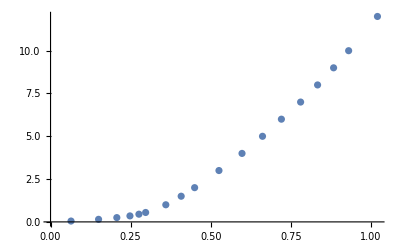

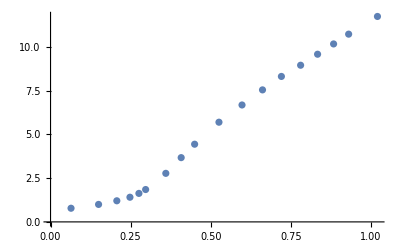

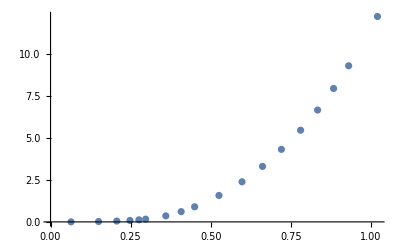

```mathematica
RvsI = Thread[{Ibulb,Rbulb}];
PvsI = Thread[{Ibulb,Pbulb}];

ListPlot[VvsI]
ListPlot[RvsI]
ListPlot[PvsI]
```

We still need to label the axes, put in titles on each of the plots, and make a caption for each. (Again, just edit what you have already written above and re-evaluate the cell.) To do this, let’s amend the code in the following way:

(Hint: The arrow is made with a space, a dash, then a greater than symbol, i.e. “ -> ” which will automatically turn into → when you press space. Also note that we put the plots in separate cells, so we can have text cell commentary below the plots. You can divide cells by right-clicking at the point where you want to divide the cell.)

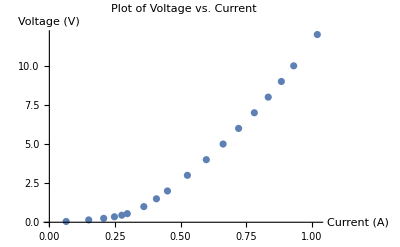

```mathematica
ListPlot[VvsI,PlotLabel->"Plot of Voltage vs. Current",AxesLabel -> {"Current (A)","Voltage (V)"}]
```

Here, you should write a caption in a text cell like: “The plot above describes the relationship between voltage and current in the light bulb, etc...” Make additional observations and analysis as you see fit.

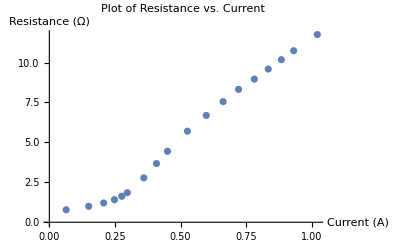

```mathematica
ListPlot[RvsI,PlotLabel->"Plot of Resistance vs. Current",AxesLabel -> {"Current (A)","Resistance (Ω)"}]
```

Once again, make a caption describing the plot.

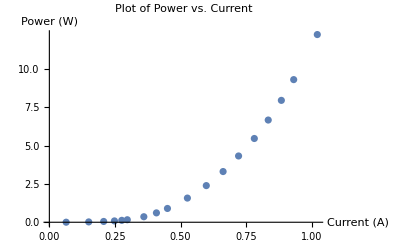

```mathematica
ListPlot[PvsI,PlotLabel->"Plot of Power vs. Current",AxesLabel -> {"Current (A)","Power (W)"}]
```

More pithy captions and comments...

Be sure to make observations about your results in text cells, and perform any additional calculations that the lab requires!

## Write Your Conclusion!

Write your conclusion in the same way you wrote your introduction -with different content of course! Be sure to spell check your document when you are finished. Wasn’t this so much fun?! ☺

## Two Things not to Forget to Attach to Your E1 Lab:

1) Your Part III worksheet, i.e. pages 7 and 8 from your lab manual. ☺
2) Your data sheet(s) for Part I. ☺